# Quartic covariant galileon

## comparison EFTCAMB (G4) with WBG implemented in EFTCAMB (c5 = 0)

Hubble parameter

```mathematica
OmegaM0=0.30964144154;
OmegaR0=8.32*10^(-5);(*10^(-5)*)(*8.32*10^(-5)*)
OmegaPhi0=1-OmegaM0-OmegaR0;
s=1;
a=.
HoverH0equation=1-x^-2(OmegaM0/a+OmegaR0/a^2)-(a/x)^(2(1+s))(OmegaPhi0); (*x is conformal H over H_0*)
Solution=NSolve[HoverH0equation==0,x]
a=1
Solution (*Looking at this I know the right solution is the fourth one*)
```

{{x→-1.37376×10^-10 √((2.20431×10^15)/a^2+(8.20366×10^18)/a-(1156.3 √(3.63412×10^24+2.70499×10^28 a+5.03351×10^31 a^2+1.44956×10^33 a^8))/a^2)},{x→1.37376×10^-10 √((2.20431×10^15)/a^2+(8.20366×10^18)/a-(1156.3 √(3.63412×10^24+2.70499×10^28 a+5.03351×10^31 a^2+1.44956×10^33 a^8))/a^2)},{x→-1.37376×10^-10 √((2.20431×10^15)/a^2+(8.20366×10^18)/a+(1156.3 √(3.63412×10^24+2.70499×10^28 a+5.03351×10^31 a^2+1.44956×10^33 a^8))/a^2)},{x→1.37376×10^-10 √((2.20431×10^15)/a^2+(8.20366×10^18)/a+(1156.3 √(3.63412×10^24+2.70499×10^28 a+5.03351×10^31 a^2+1.44956×10^33 a^8))/a^2)}}

1

{{x→0.-0.830828 ⅈ},{x→0.+0.830828 ⅈ},{x→-1.},{x→1.}}

```mathematica
a=.
HconfOverH0=1.3737596844821898*^-10 √((2.204305562192591*^15)/a^2+(8.203658075384063*^18)/a+1/a^2 1156.3040257648504 √(3.6341221247197686*^24+2.7049875322851848*^28 a+5.033511050748268*^31 a^2+1.4495567633184376*^33 a^8))
```

1.37376×10^-10 √((2.20431×10^15)/a^2+(8.20366×10^18)/a+(1156.3 √(3.63412×10^24+2.70499×10^28 a+5.03351×10^31 a^2+1.44956×10^33 a^8))/a^2)

```mathematica
dataEFTCAMBadotoa=Import[FileNameJoin[{NotebookDirectory[],"fort.31"}]];
```

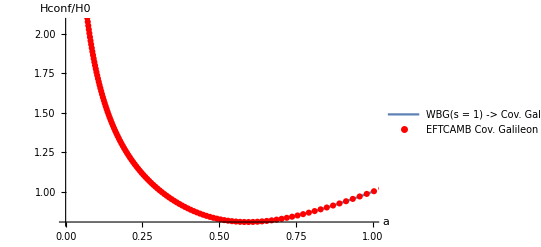

```mathematica
nbPlotH=Plot[{HconfOverH0},{a,0,1}, PlotLegends->{"WBG(s = 1) -> Cov. Galileon"}, AxesLabel->{Style["a",FontSize->20],Style["Hconf/H0",FontSize->20]}];
EFTCAMBPlotH = ListPlot[
dataEFTCAMBadotoa⟦All,{1,2}⟧
,Joined->False
,PlotMarkers->Automatic, PlotRange->{{0,1},{-0.15,2}}, PlotStyle->Red, PlotLegends->{"EFTCAMB Cov. Galileon"}
];
Show[nbPlotH,EFTCAMBPlotH]
```

## HPrime

```mathematica
HPrimeOverH0 =D[HconfOverH0 ,a]//Expand//Simplify
HPrimetheoryPlot=Plot[{HPrimeOverH0},{a,0,1}, PlotLegends->{"WBG(s = 1) -> Cov. Galileon"}, AxesLabel->{Style["a",FontSize->20],Style["HconfPrime(a)/H0",FontSize->20]}];

dataEFTCAMBHPrime=Import[FileNameJoin[{NotebookDirectory[],"fort.31"}]];
HPrimePWBGPlot = ListPlot[
dataEFTCAMBHPrime⟦All,{1,3}⟧
,Joined->False
,PlotMarkers->Automatic, PlotStyle->Red, PlotLegends->{"EFTCAMB Cov. Galileon"}, PlotLabel->"HconfPrime(a)/H0"
];

Show[HPrimetheoryPlot,HPrimePWBGPlot]
```

(-5.77274×10^17-3.99783×10^24 a^2+2.3026×10^26 a^8-302819. √(3.63412×10^24+2.70499×10^28 a+5.03351×10^31 a^2+1.44956×10^33 a^8)+a (-3.22262×10^21-5.63493×10^8 √(3.63412×10^24+2.70499×10^28 a+5.03351×10^31 a^2+1.44956×10^33 a^8)))/(a^3 √(3.63412×10^24+2.70499×10^28 a+5.03351×10^31 a^2+1.44956×10^33 a^8) √((2.20431×10^15+8.20366×10^18 a+1156.3 √(3.63412×10^24+2.70499×10^28 a+5.03351×10^31 a^2+1.44956×10^33 a^8))/a^2))

-Graphics-

## Chi

```mathematica
a=.
XoverXds = (   (1-OmegaM0-OmegaR0)^( 1/(2(s+1)) ) HconfOverH0^(-1) a )^(1/q)/.s->1/.p->1/.q->1/2//PowerExpand//Simplify
XPrimeoverXds = D[XoverXds,a]/.s->1/.p->1/.q->1/2//PowerExpand//Simplify
```

(4.4024×10^19 a^4)/(2.20431×10^15+8.20366×10^18 a+1156.3 √(3.63412×10^24+2.70499×10^28 a+5.03351×10^31 a^2+1.44956×10^33 a^8))

(a^3 (3.8817×10^35+1.08347×10^39 a-(2.54526×10^22 a (2.70499×10^28+1.0067×10^32 a+1.15965×10^34 a^7))/(√(3.63412×10^24+2.70499×10^28 a+5.03351×10^31 a^2+1.44956×10^33 a^8))+2.03621×10^23 √(3.63412×10^24+2.70499×10^28 a+5.03351×10^31 a^2+1.44956×10^33 a^8)))/((2.20431×10^15+8.20366×10^18 a+1156.3 √(3.63412×10^24+2.70499×10^28 a+5.03351×10^31 a^2+1.44956×10^33 a^8))^2)

```mathematica
dataEFTCAMBChi=Import[FileNameJoin[{NotebookDirectory[],"fort.32"}]];
dataEFTCAMBChiP=Import[FileNameJoin[{NotebookDirectory[],"fort.333"}]];
```

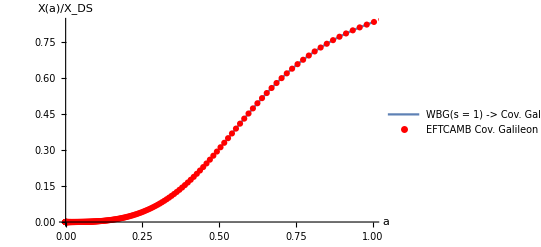

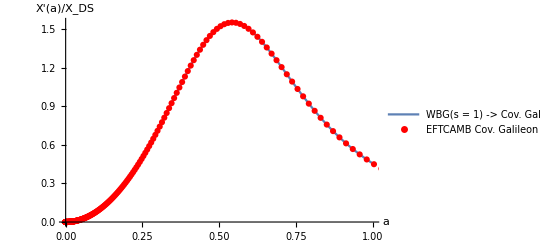

```mathematica
XtheoryPlot=Plot[{XoverXds},{a,0,1}, PlotLegends->{"WBG(s = 1) -> Cov. Galileon"}, AxesLabel->{Style["a",FontSize->20],Style["Χ(a)/Χ_DS",FontSize->20]}];
XPtheoryPlot=Plot[{XPrimeoverXds},{a,0,1}, PlotLegends->{"WBG(s = 1) -> Cov. Galileon"}, AxesLabel->{Style["a",FontSize->20],Style["Χ'(a)/Χ_DS",FontSize->20]}];
XWBGPlot = ListPlot[
dataEFTCAMBChi⟦All,{1,2}⟧
,Joined->False
,PlotMarkers->Automatic, PlotRange->{{0,1},{-0.15,2}}, PlotStyle->Red, PlotLegends->{"EFTCAMB Cov. Galileon"}, PlotLabel->"Chi(a)"
];
XPWBGPlot = ListPlot[
dataEFTCAMBChiP⟦All,{1,2}⟧
,Joined->False
,PlotMarkers->Automatic, PlotStyle->Red, PlotRange->{{0,1},{-0.15,2}}, PlotLegends->{"EFTCAMB Cov. Galileon"}, PlotLabel->"ChiP(a)"
];
Show[XtheoryPlot,XWBGPlot]
Show[XPtheoryPlot,XPWBGPlot]
```

## PhiPrime

(1.33264×10^20 √(a^4/(2.20431×10^15+8.20366×10^18 a+1156.3 √(3.63412×10^24+2.70499×10^28 a+5.03351×10^31 a^2+1.44956×10^33 a^8))))/(√((2.20431×10^15+8.20366×10^18 a+1156.3 √(3.63412×10^24+2.70499×10^28 a+5.03351×10^31 a^2+1.44956×10^33 a^8))/a^2))

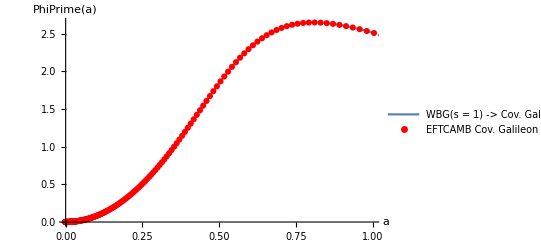

```mathematica
PhiPrime = Sqrt[-XoverXds XDS]/(HconfOverH0 ) /.XDS->-7.613018601091973 //Expand//Simplify
PhiPrimetheoryPlot=Plot[{PhiPrime},{a,0,1}, PlotLegends->{"WBG(s = 1) -> Cov. Galileon"}, AxesLabel->{Style["a",FontSize->20],Style["PhiPrime(a)",FontSize->20]}];

dataEFTCAMBPhiPrime=Import[FileNameJoin[{NotebookDirectory[],"fort.33"}]];
PhiPrimePWBGPlot = ListPlot[
dataEFTCAMBPhiPrime⟦All,{1,2}⟧
,Joined->False
,PlotMarkers->Automatic, PlotStyle->Red, PlotLegends->{"EFTCAMB Cov. Galileon"}, PlotLabel->"PhiPrime(a)"
];

Show[PhiPrimetheoryPlot,PhiPrimePWBGPlot]
```

## PhiPrimePrime

(√(a^4/(2.20431×10^15+8.20366×10^18 a+1156.3 √(3.63412×10^24+2.70499×10^28 a+5.03351×10^31 a^2+1.44956×10^33 a^8))) (5.5394×10^57+1.90361×10^68 a^3+1.37051×10^69 a^9+2.90578×10^45 √(3.63412×10^24+2.70499×10^28 a+5.03351×10^31 a^2+1.44956×10^33 a^8)+a^8 (7.36508×10^65-1.93174×10^53 √(3.63412×10^24+2.70499×10^28 a+5.03351×10^31 a^2+1.44956×10^33 a^8))+a (5.49753×10^61+1.80239×10^49 √(3.63412×10^24+2.70499×10^28 a+5.03351×10^31 a^2+1.44956×10^33 a^8))+a^2 (1.79024×10^65+2.68314×10^52 √(3.63412×10^24+2.70499×10^28 a+5.03351×10^31 a^2+1.44956×10^33 a^8))))/(a √(3.63412×10^24+2.70499×10^28 a+5.03351×10^31 a^2+1.44956×10^33 a^8) (1.90634×10^12+7.09472×10^15 a+1. √(3.63412×10^24+2.70499×10^28 a+5.03351×10^31 a^2+1.44956×10^33 a^8))^2 √((2.20431×10^15+8.20366×10^18 a+1156.3 √(3.63412×10^24+2.70499×10^28 a+5.03351×10^31 a^2+1.44956×10^33 a^8))/a^2))

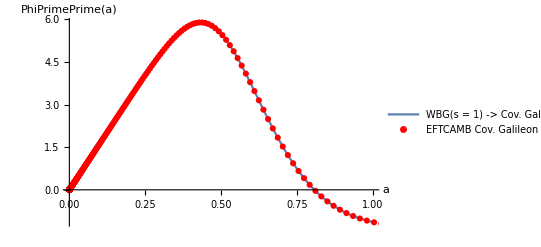

```mathematica
PhiPrimePrime = D[Sqrt[-XoverXds XDS]/(HconfOverH0 ),a] /.XDS->-7.613018601091973 //Expand//Simplify
PhiPrimePrimetheoryPlot=Plot[{PhiPrimePrime},{a,0,1}, PlotLegends->{"WBG(s = 1) -> Cov. Galileon"}, AxesLabel->{Style["a",FontSize->20],Style["PhiPrimePrime(a)",FontSize->20]}];

dataEFTCAMBPhiPrimePrime=Import[FileNameJoin[{NotebookDirectory[],"fort.33"}]];
PhiPrimePrimePWBGPlot = ListPlot[
dataEFTCAMBPhiPrimePrime⟦All,{1,3}⟧
,Joined->False
,PlotMarkers->Automatic, PlotStyle->Red, PlotLegends->{"EFTCAMB Cov. Galileon"}, PlotLabel->"PhiPrime(a)"
];

Show[PhiPrimePrimetheoryPlot,PhiPrimePrimePWBGPlot]
```

## EFT FUNCTIONS

```mathematica
p=.
q=.
s=.
CovGal = {s->1,p->1, q->1/2}
```

{s→1,p→1,q→1/2}

```mathematica
c4=.
c5=0;
DeSitterFP = {Subscript[c, 2]->3-6 Subscript[c, 4]-24 Subscript[c, 5]+12 Subscript[c, 4] p+24 Subscript[c, 4] q,Subscript[c, 3]->(√2 p)/(-1+2 p+2 q)-(4 √2 Subscript[c, 4] p)/(-1+2 p+2 q)-(16 √2 Subscript[c, 5] p)/(-1+2 p+2 q)+(8 √2 Subscript[c, 4] p^2)/(-1+2 p+2 q)-(4 √2 Subscript[c, 4] q)/(-1+2 p+2 q)-(16 √2 Subscript[c, 5] q)/(-1+2 p+2 q)+(24 √2 Subscript[c, 4] p q)/(-1+2 p+2 q)+(16 √2 Subscript[c, 4] q^2)/(-1+2 p+2 q)}
```

{c2→3-6 c4+12 c4 p+24 c4 q,c3→(√2 p)/(-1+2 p+2 q)-(4 √2 c4 p)/(-1+2 p+2 q)+(8 √2 c4 p^2)/(-1+2 p+2 q)-(4 √2 c4 q)/(-1+2 p+2 q)+(24 √2 c4 p q)/(-1+2 p+2 q)+(16 √2 c4 q^2)/(-1+2 p+2 q)}

```mathematica
Hc=HconfOverH0 H0//Simplify;
HcP = D[Hc,a]//Simplify;
HcPP = D[HcP,a]//Simplify;
HcPPP = D[HcPP,a]//Simplify;
X = XoverXds Xds//Simplify;
PhiP = Sqrt[-X]/Hc//Simplify;
PhiPP = D[PhiP,a]//Simplify;
PhiPPP = D[PhiPP,a]//Simplify;
PhiPPPP = D[PhiPPP,a]//Simplify;
```

```mathematica
CGSubstitute = {p->1, q->1/2,Subscript[χ, DS]->Xds,XDS->Xds,Hconf[a]->Hc,ℋ'[a]->HcP,ℋ''[a]->HcPP, Derivative[3][ℋ][a]->HcPPP,PhiPrime[a]-> PhiP, PhiPrimePrime[a]->PhiPP,PhiPrimePrimePrime[a] ->PhiPPP,PhiPrimePrimePrimePrime[a] ->PhiPPPP,OverDot[ȧ]->adotdot, ȧ->adot,Hds-> H0(1-OmegaM0-OmegaR0)^(1/4)};
```

```mathematica
dataEFTCAMB=Import[FileNameJoin[{NotebookDirectory[],"QuarticGalileon_BackgroundEFT.dat"}]]
```

{{1.×10^-10,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00010001,0.,0.,-9.58378×10^-26,-7.1621×10^-21,-4.59973×10^-16,-2.46485×10^-11,2.48833×10^-28,2.11744×10^-29,9.6274×10^-28,8.41109×10^-29},{0.00020002,0.,0.,-1.54089×10^-23,-5.52218×10^-19,-1.68443×10^-14,-4.22713×10^-10,9.42325×10^-27,4.07525×10^-28,3.96389×10^-26,1.80036×10^-27},29995,{1.×10^-10,0.,0.,-1.75374×10^-73,-1.40299×10^-62,-9.82093×10^-52,-5.89256×10^-41,5.04184×10^-64,4.33759×10^-59,1.76464×10^-63,1.51816×10^-58},{1.×10^-10,0.,0.,-1.75374×10^-73,-1.40299×10^-62,-9.82093×10^-52,-5.89256×10^-41,5.04184×10^-64,4.33759×10^-59,1.76464×10^-63,1.51816×10^-58}}
 |  |  |  |

## OMEGA

-(3.28906×10^38 a^8)/((2.20431×10^15+8.20366×10^18 a+1156.3 √(3.63412×10^24+2.70499×10^28 a+5.03351×10^31 a^2+1.44956×10^33 a^8))^2)

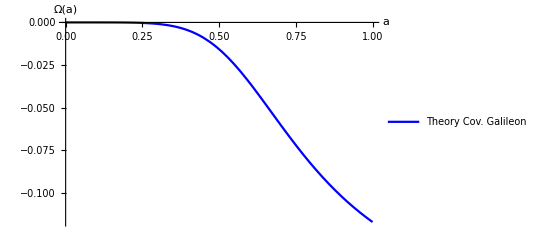

```mathematica
Omega=-1-2 (-1)^(-p (1+1/s)) Subscript[c, 4] Subscript[χ, DS]^(-p (1+1/s)) ℋ[a]^((2 p (1+s))/s) φ'[a]^((2 p (1+s))/s);
OmegaCG=(Omega+1)/.DeSitterFP/.CGSubstitute/.c4->0.08485200961571562/.s->1//PowerExpand//Simplify
OmegaTheoryPlot=Plot[OmegaCG,{a,0,1}, PlotStyle->Blue, PlotLegends->{"Theory Cov. Galileon"}, AxesLabel->{Style["a",FontSize->20],Style["Ω(a)",FontSize->20]}]
```

```mathematica
OmegaData = Import[FileNameJoin[{NotebookDirectory[],"fort.35"}]];
```

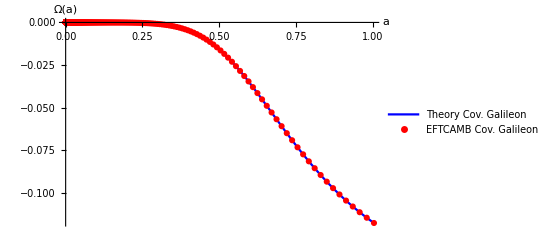

```mathematica
OmegaWBGPlot=ListPlot[
OmegaData⟦All,{1,2}⟧
,Joined->False
,PlotMarkers->Automatic, PlotStyle->Red,PlotRange->{{0,1},{-0.15,0}},  PlotLabel->"Omega(a)", PlotLegends->{"EFTCAMB Cov. Galileon"}
];
Show[OmegaTheoryPlot,OmegaWBGPlot]
```

(a^7 (-1.03962×10^83-1.49582×10^97 a^4-3.23077×10^98 a^10+9.71334×10^83 a^16-5.45352×10^70 √(3.63412×10^24+2.70499×10^28 a+5.03351×10^31 a^2+1.44956×10^33 a^8)+a^9 (-2.02557×10^95-1.51792×10^82 √(3.63412×10^24+2.70499×10^28 a+5.03351×10^31 a^2+1.44956×10^33 a^8))+a^3 (-1.74167×10^94-2.10836×10^81 √(3.63412×10^24+2.70499×10^28 a+5.03351×10^31 a^2+1.44956×10^33 a^8))+a^8 (-3.11009×10^91-5.43816×10^78 √(3.63412×10^24+2.70499×10^28 a+5.03351×10^31 a^2+1.44956×10^33 a^8))+a^2 (-7.55975×10^90-1.88837×10^78 √(3.63412×10^24+2.70499×10^28 a+5.03351×10^31 a^2+1.44956×10^33 a^8))+a (-1.45092×10^87-5.58142×10^74 √(3.63412×10^24+2.70499×10^28 a+5.03351×10^31 a^2+1.44956×10^33 a^8))))/(√(3.63412×10^24+2.70499×10^28 a+5.03351×10^31 a^2+1.44956×10^33 a^8) (1.90634×10^12+7.09472×10^15 a+1. √(3.63412×10^24+2.70499×10^28 a+5.03351×10^31 a^2+1.44956×10^33 a^8))^5)

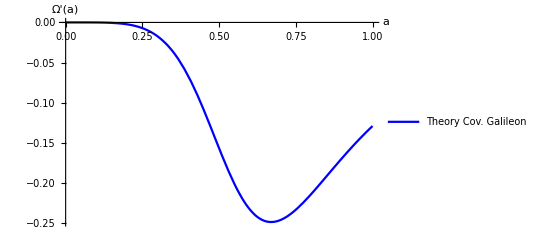

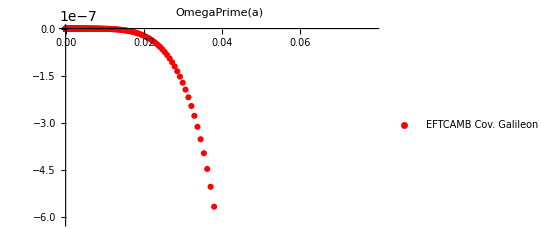

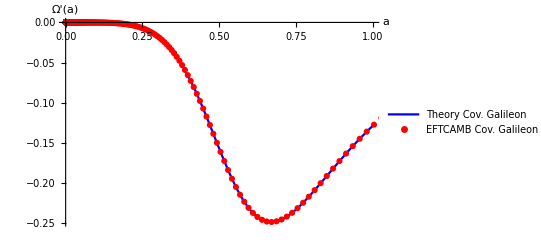

```mathematica
OmegaPrime = -(4 (-1)^(-(p (2+s))/s) Subscript[c, 4] p (2+s) Subscript[χ, DS]^(-(p (2+s))/s) ℋ[a]^(-1+(2 p (2+s))/s) φ'[a]^(-1+(2 p (2+s))/s) (ℋ[a] φ''[a]+φ'[a] ℋ'[a]))/s;
OmegaPrimeCG = OmegaPrime/.DeSitterFP/.CGSubstitute/.s->2/.Xds->-7.613018601091973 H0^2/.c4->0.08485200961571562//PowerExpand//Simplify
OmegaPTheoryPlot=Plot[OmegaPrimeCG,{a,0,1}, PlotStyle->Blue,PlotLegends->{"Theory Cov. Galileon"}, AxesLabel->{Style["a",FontSize->20],Style["Ω'(a)",FontSize->20]}]


OmegaPWBGPlot=ListPlot[
OmegaData⟦All,{1,3}⟧
,Joined->False
,PlotMarkers->Automatic, PlotStyle->Red ,PlotLabel->"OmegaPrime(a)", PlotLegends->{"EFTCAMB Cov. Galileon"}
]

Show[OmegaPTheoryPlot,OmegaPWBGPlot]
```

## c(a)

(0.+0. ⅈ)+((4.7773×10^74+0. ⅈ) a^6)/(1)^5+((1) a^7)/(1)^5+671+1/1+1/((1)^4 1^2)-((1.14401×10^82+0. ⅈ) a^21 √(3.63412×10^24+2.70499×10^28 a+22 1+1.44956×10^33 a^8) √(a^4/(2.20431×10^15+22 a+1156.3 √1)) √((2.20431×10^15+8.20366×10^18 a+1156.3 √(3.63412×10^24+2.70499×10^28 a+1+1.44956×10^33 a^8))/a^2))/((1.90634×10^12+7.09472×10^15 a+1. √(3.63412×10^24+2.70499×10^28 a+5.03351×10^31 a^2+1.44956×10^33 a^8))^4 (2.20431×10^15+8.20366×10^18 a+1156.3 √1)^2)
 |  |  |  |

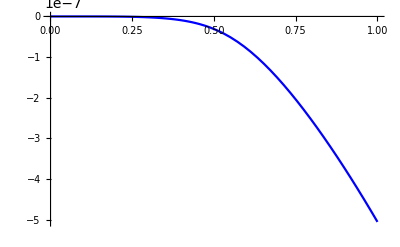

```mathematica
(*this one I take without substituting XD->-XDS, it works*)
c1=1/(2 a^2 s^2 φ'[a]^2)(-1)^(-(3 p (1+s))/s)  Subscript[χ, DS]^(-(3 p (1+s))/s) (-2 (-1)^((p (3+2 s))/s) a^2 Subscript[c, 2] Subscript[H, DS]^2 p s^2 Subscript[χ, DS]^((p (3+2 s))/s) ℋ[a]^(2 p) φ'[a]^(2+2 p)+(-1)^((2 p (1+s))/s) √2 a Subscript[c, 3] Subscript[H, DS] s (-s+2 p (1+s)) Subscript[χ, DS]^((2 p (1+s))/s) ℋ[a]^(1+(2 p (1+s))/s) φ'[a]^(1+(2 p (1+s))/s) (3 φ'[a]-a φ''[a])-4 (-1)^(p (2+1/s)) Subscript[χ, DS]^(p (2+1/s)) ℋ[a]^(2+(2 p (2+s))/s) φ'[a]^((2 p (2+s))/s) ((-28 Subscript[c, 5] s^2+Subscript[c, 4] p (2+s) (-s+6 p (2+s))) φ'[a]^2-a^2 Subscript[c, 4] p (2+s) (-s+2 p (2+s)) φ''[a]^2-a p (2+s) φ'[a] ((-3 Subscript[c, 4] s-8 Subscript[c, 5] s+4 Subscript[c, 4] p (2+s)) φ''[a]+a Subscript[c, 4] s φ'''[a]))+(-1)^(1+(2 p (1+s))/s) √2 a^2 Subscript[c, 3] Subscript[H, DS] s (-s+2 p (1+s)) Subscript[χ, DS]^((2 p (1+s))/s) ℋ[a]^((2 p (1+s))/s) φ'[a]^(2 (1+p+p/s)) ℋ'[a]+8 (-1)^(p (2+1/s)) a^2 Subscript[c, 4] p^2 (2+s)^2 Subscript[χ, DS]^(p (2+1/s)) ℋ[a]^((2 p (2+s))/s) φ'[a]^(2+(2 p (2+s))/s) ℋ'[a]^2+4 (-1)^(p (2+1/s)) a Subscript[χ, DS]^(p (2+1/s)) ℋ[a]^(1+(2 p (2+s))/s) φ'[a]^(1+(2 p (2+s))/s) (a Subscript[c, 4] p (2+s) (s+4 p (2+s)) φ''[a] ℋ'[a]+φ'[a] ((-4 Subscript[c, 5] s (s+2 p (2+s))+Subscript[c, 4] p (2+s) (-s+4 p (2+s))) ℋ'[a]+a Subscript[c, 4] p s (2+s) ℋ''[a])))*a^2;
cCG1=c1/.DeSitterFP/.CGSubstitute/.s->2/.Xds->-7.613018601091973 H0^2/.c4->0.08485200961571562//Expand;
cCG21=cCG1/.XDS->-7.613018601091973 H0^2/.H0-> 67.66/(2.99792458 10^5)
c1TheoryPlot=Plot[%,{a,0.001,1}, PlotStyle->Blue]
```

```mathematica
(*this one I take after substituting XD->-XDS, it does not work*)
c=1/(2 s^2 PhiPrime[a]^2)(-1)^(-(6 p (1+s))/s) XDS^(-(3 p (1+s))/s) (-2 (-1)^(p (4+6/s)) a^2 c2 Hds^2 p s^2 XDS^((p (3+2 s))/s) Hconf[a]^(2 p) PhiPrime[a]^(2+2 p)+(-1)^((4 p (1+s))/s) √2 a c3 Hds s (-s+2 p (1+s)) XDS^((2 p (1+s))/s) Hconf[a]^(1+(2 p (1+s))/s) PhiPrime[a]^(1+(2 p (1+s))/s) (3 PhiPrime[a]-a PhiPrimePrime[a])-4 (-1)^(2 p (2+1/s)) XDS^(p (2+1/s)) Hconf[a]^(2+(2 p (2+s))/s) PhiPrime[a]^((2 p (2+s))/s) ((-28 c5 s^2+c4 p (2+s) (-s+6 p (2+s))) PhiPrime[a]^2-a^2 c4 p (2+s) (-s+2 p (2+s)) PhiPrimePrime[a]^2-a p (2+s) PhiPrime[a] ((-3 c4 s-8 c5 s+4 c4 p (2+s)) PhiPrimePrime[a]+a c4 s PhiPrimePrimePrime[a]))+(-1)^(1+(4 p (1+s))/s) √2 a^2 c3 Hds s (-s+2 p (1+s)) XDS^((2 p (1+s))/s) Hconf[a]^((2 p (1+s))/s) PhiPrime[a]^(2 (1+p+p/s)) Hconf'[a]+8 (-1)^(2 p (2+1/s)) a^2 c4 p^2 (2+s)^2 XDS^(p (2+1/s)) Hconf[a]^((2 p (2+s))/s) PhiPrime[a]^(2+(2 p (2+s))/s) Hconf'[a]^2+4 (-1)^(2 p (2+1/s)) a XDS^(p (2+1/s)) Hconf[a]^(1+(2 p (2+s))/s) PhiPrime[a]^(1+(2 p (2+s))/s) (a c4 p (2+s) (s+4 p (2+s)) PhiPrimePrime[a] Hconf'[a]+PhiPrime[a] ((-4 c5 s (s+2 p (2+s))+c4 p (2+s) (-s+4 p (2+s))) Hconf'[a]+a c4 p s (2+s) Hconf''[a])));
cCG=c/.DeSitterFP/.CGSubstitute/.s->2/.Xds->7.613018601091973 H0^2/.c4->0.08485200961571562//Expand;
cCG2=cCG/.H0-> 67.66/(2.99792458 10^5)
cTheoryPlot=Plot[%,{a,0.001,1}, PlotStyle->Blue]

cCG2/.a->0.1
```

0.+(4.7773×10^74 a^6)/(1)^5+1/1^5+689+(1.14401×10^82 a^21 √(3.63412×10^24+2.70499×10^28 a+22 1+1.44956×10^33 a^8) √(-a^4/(2.20431×10^15+8.20366×10^18 a+1156.3 √1)) √((2.20431×10^15+8.20366×10^18 a+1156.3 √(3.63412×10^24+2.70499×10^28 a+1+1.44956×10^33 a^8))/a^2))/((1.90634×10^12+7.09472×10^15 a+1. √(3.63412×10^24+2.70499×10^28 a+5.03351×10^31 a^2+1.44956×10^33 a^8))^4 (2.20431×10^15+8.20366×10^18 a+1156.3 √1)^2)
 |  |  |  |

-Graphics-

5.99729×10^-12+4.28933×10^-12 ⅈ

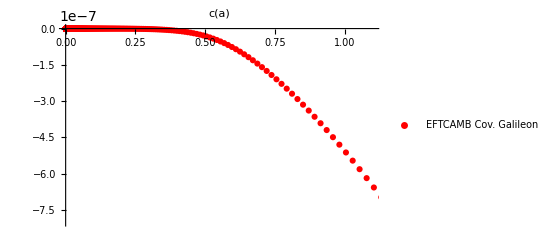

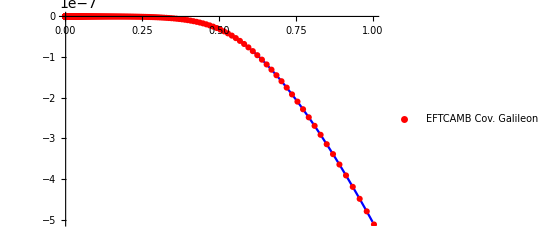

```mathematica
cData = Import[FileNameJoin[{NotebookDirectory[],"fort.35"}]];
cWBGPlot=ListPlot[
cData⟦All,{1,4}⟧
,Joined->False
,PlotMarkers->Automatic, PlotStyle->Red,PlotRange->{{0,1.1},{0,-8*10^(-7)}},  PlotLabel->"c(a)", PlotLegends->{"EFTCAMB Cov. Galileon"}
]
Show[c1TheoryPlot,cWBGPlot]
```

## cDot

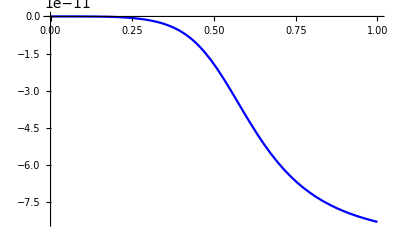

-8.29188×10^-11

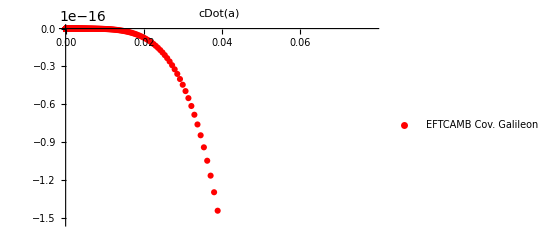

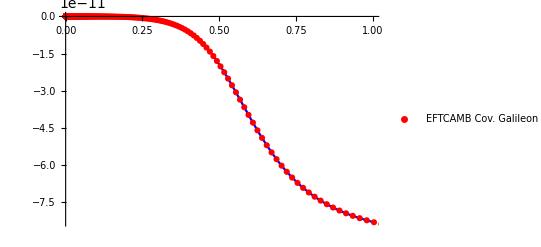

```mathematica
cDot = 1/(2  s^3 φ'[a]^3)(-1)^(-(3 p (1+s))/s)  Subscript[χ, DS]^(-(3 p (1+s))/s) (-4 (-1)^((p (3+2 s))/s) a^3 Subscript[c, 2] Subscript[H, DS]^2 p^2 s^3 Subscript[χ, DS]^((p (3+2 s))/s) ℋ[a]^(1+2 p) φ'[a]^(2+2 p) φ''[a]+(-1)^(1+(2 p (1+s))/s) √2 a Subscript[c, 3] Subscript[H, DS] s (-s+2 p (1+s)) Subscript[χ, DS]^((2 p (1+s))/s) ℋ[a]^(2 (1+p+p/s)) φ'[a]^(1+(2 p (1+s))/s) (3 s φ'[a]^2+a^2 (-s+2 p (1+s)) φ''[a]^2+a φ'[a] (-6 p (1+s) φ''[a]+a s φ'''[a]))-4 (-1)^(p (2+1/s)) Subscript[χ, DS]^(p (2+1/s)) ℋ[a]^(3+(2 p (2+s))/s) φ'[a]^((2 p (2+s))/s) (2 s (28 Subscript[c, 5] s^2-Subscript[c, 4] p (2+s) (-s+6 p (2+s))) φ'[a]^3-2 a^3 Subscript[c, 4] p (2+s) (s^2-3 p s (2+s)+2 p^2 (2+s)^2) φ''[a]^3-a^2 p (2+s) (-s+2 p (2+s)) φ'[a] φ''[a] ((-3 Subscript[c, 4] s-8 Subscript[c, 5] s+4 Subscript[c, 4] p (2+s)) φ''[a]+3 a Subscript[c, 4] s φ'''[a])+a p (2+s) φ'[a]^2 ((-64 Subscript[c, 5] s^2+Subscript[c, 4] (-3 s^2+2 p s (2+s)+12 p^2 (2+s)^2)) φ''[a]-a s ((-3 Subscript[c, 4] s-8 Subscript[c, 5] s+4 Subscript[c, 4] p (2+s)) φ'''[a]+a Subscript[c, 4] s φ''''[a])))-4 (-1)^((p (3+2 s))/s) a^3 Subscript[c, 2] Subscript[H, DS]^2 p^2 s^3 Subscript[χ, DS]^((p (3+2 s))/s) ℋ[a]^(2 p) φ'[a]^(3+2 p) ℋ'[a]-2 (-1)^((2 p (1+s))/s) √2 a^3 Subscript[c, 3] Subscript[H, DS] p s (1+s) (-s+2 p (1+s)) Subscript[χ, DS]^((2 p (1+s))/s) ℋ[a]^((2 p (1+s))/s) φ'[a]^(3+(2 p (1+s))/s) ℋ'[a]^2+16 (-1)^(p (2+1/s)) a^3 Subscript[c, 4] p^3 (2+s)^3 Subscript[χ, DS]^(p (2+1/s)) ℋ[a]^((2 p (2+s))/s) φ'[a]^(3+(2 p (2+s))/s) ℋ'[a]^3+(-1)^((2 p (1+s))/s) √2 a^2 Subscript[c, 3] Subscript[H, DS] s (-s+2 p (1+s)) Subscript[χ, DS]^((2 p (1+s))/s) ℋ[a]^(1+(2 p (1+s))/s) φ'[a]^(2 (1+p+p/s)) (-a (s+4 p (1+s)) φ''[a] ℋ'[a]+φ'[a] (3 (s+2 p (1+s)) ℋ'[a]-a s ℋ''[a]))+4 (-1)^(p (2+1/s)) a^2 Subscript[χ, DS]^(p (2+1/s)) ℋ[a]^(1+(2 p (2+s))/s) φ'[a]^(2+(2 p (2+s))/s) ℋ'[a] (a Subscript[c, 4] p (2+s) (s^2+6 p s (2+s)+12 p^2 (2+s)^2) φ''[a] ℋ'[a]+φ'[a] ((s+2 p (2+s)) (-4 Subscript[c, 5] s (s+2 p (2+s))+Subscript[c, 4] p (2+s) (-s+4 p (2+s))) ℋ'[a]+a Subscript[c, 4] p s (2+s) (s+6 p (2+s)) ℋ''[a]))+4 (-1)^(p (2+1/s)) a Subscript[χ, DS]^(p (2+1/s)) ℋ[a]^(2+(2 p (2+s))/s) φ'[a]^(1+(2 p (2+s))/s) (3 a^2 Subscript[c, 4] p (2+s) (-s^2+4 p^2 (2+s)^2) φ''[a]^2 ℋ'[a]+a p (2+s) φ'[a] (3 a Subscript[c, 4] s (s+2 p (2+s)) φ'''[a] ℋ'[a]+φ''[a] (2 (-4 Subscript[c, 5] s (3 s+4 p (2+s))+Subscript[c, 4] (-3 s^2+8 p^2 (2+s)^2)) ℋ'[a]+a Subscript[c, 4] s (s+6 p (2+s)) ℋ''[a]))-φ'[a]^2 ((-4 Subscript[c, 5] s^2 (15 s+16 p (2+s))+Subscript[c, 4] p (2+s) (-3 s^2+14 p s (2+s)+12 p^2 (2+s)^2)) ℋ'[a]+a s ((4 Subscript[c, 5] s (s+2 p (2+s))-Subscript[c, 4] p (2+s) (-s+4 p (2+s))) ℋ''[a]-a Subscript[c, 4] p s (2+s) Derivative[3][ℋ][a]))))//Simplify;
cDotCG = %/.DeSitterFP/.CGSubstitute/.s->2/.Xds->-7.613018601091973 H0^2/.H0-> 67.66/(2.99792458 10^5)/.c4->0.08485200961571562//Expand;
cDotTheoryPlot=Plot[%,{a,0,1},PlotStyle->Blue]
cDotCG/.a->1

cDotWBGPlot=ListPlot[
cData⟦All,{1,5}⟧
,Joined->False
,PlotMarkers->Automatic, PlotStyle->Red,  PlotLabel->"cDot(a)", PlotLegends->{"EFTCAMB Cov. Galileon"}
]

Show[cDotTheoryPlot,cDotWBGPlot]
```

## Lambda(a)

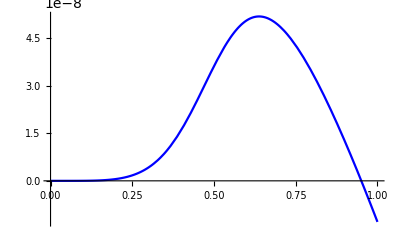

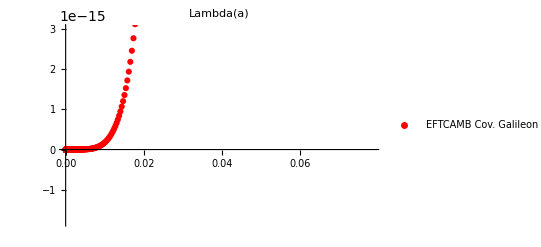

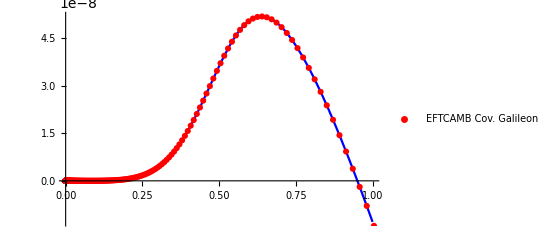

```mathematica
Leftfunct = 1/(s^2 φ'[a]^2)(-1)^(-(3 p (1+s))/s) Subscript[χ, DS]^(-(3 p (1+s))/s) ((-1)^(1+p (2+3/s)) a^2 Subscript[c, 2] Subscript[H, DS]^2 s^2 Subscript[χ, DS]^((p (3+2 s))/s) ℋ[a]^(2 p) φ'[a]^(2+2 p)+(-1)^(1+(2 p (1+s))/s) √2 a^2 Subscript[c, 3] Subscript[H, DS] s (-s+2 p (1+s)) Subscript[χ, DS]^((2 p (1+s))/s) ℋ[a]^(1+(2 p (1+s))/s) φ'[a]^(1+(2 p (1+s))/s) φ''[a]+4 (-1)^(p (2+1/s)) Subscript[χ, DS]^(p (2+1/s)) ℋ[a]^(2+(2 p (2+s))/s) φ'[a]^((2 p (2+s))/s) (s (-2 Subscript[c, 5] s+Subscript[c, 4] p (2+s)) φ'[a]^2+a^2 Subscript[c, 4] p (2+s) (-s+2 p (2+s)) φ''[a]^2+a p (2+s) φ'[a] (4 (-2 Subscript[c, 5] s+Subscript[c, 4] p (2+s)) φ''[a]+a Subscript[c, 4] s φ'''[a]))+(-1)^(1+(2 p (1+s))/s) √2 a^2 Subscript[c, 3] Subscript[H, DS] s (-s+2 p (1+s)) Subscript[χ, DS]^((2 p (1+s))/s) ℋ[a]^((2 p (1+s))/s) φ'[a]^(2 (1+p+p/s)) ℋ'[a]+8 (-1)^(p (2+1/s)) a^2 Subscript[c, 4] p^2 (2+s)^2 Subscript[χ, DS]^(p (2+1/s)) ℋ[a]^((2 p (2+s))/s) φ'[a]^(2+(2 p (2+s))/s) ℋ'[a]^2+4 (-1)^(p (2+1/s)) a Subscript[χ, DS]^(p (2+1/s)) ℋ[a]^(1+(2 p (2+s))/s) φ'[a]^(1+(2 p (2+s))/s) (a Subscript[c, 4] p (2+s) (s+4 p (2+s)) φ''[a] ℋ'[a]+φ'[a] (2 (s+2 p (2+s)) (-2 Subscript[c, 5] s+Subscript[c, 4] p (2+s)) ℋ'[a]+a Subscript[c, 4] p s (2+s) ℋ''[a])))//Simplify;

LeftCG = Leftfunct/.DeSitterFP/.CGSubstitute/.s->2/.Xds->-7.613018601091973 H0^2/.H0-> 67.66/(2.99792458 10^5)/.c4->0.08485200961571562//Expand;
LambdaTheoryPlot=Plot[LeftCG,{a,0,1},PlotStyle->Blue]

LambdaData = Import[FileNameJoin[{NotebookDirectory[],"fort.35"}]];
LambdaWBGPlot=ListPlot[
LambdaData⟦All,{1,6}⟧
,Joined->False
,PlotMarkers->Automatic, PlotStyle->Red,  PlotLabel->"Lambda(a)", PlotLegends->{"EFTCAMB Cov. Galileon"}
]

Show[LambdaTheoryPlot,LambdaWBGPlot]
```

## LambdaDot

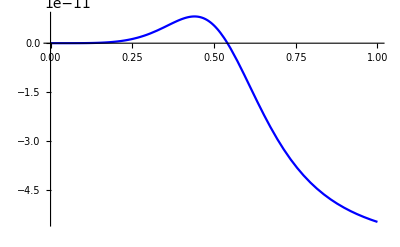

-5.48363×10^-11

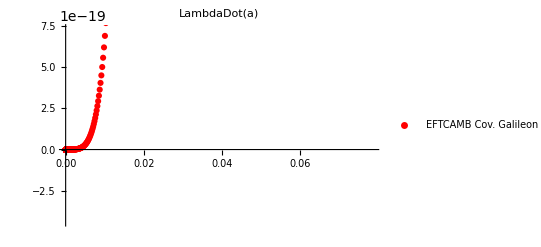

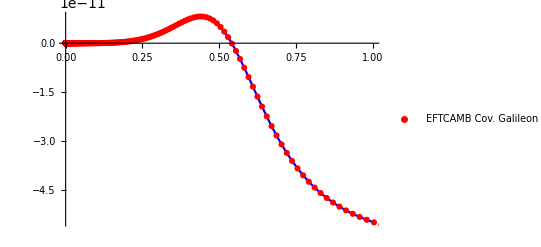

```mathematica
LDot = 1/(s^3 φ'[a]^3)(-1)^(-(3 p (1+s))/s) Subscript[χ, DS]^(-(3 p (1+s))/s) (-2 (-1)^(p (2+3/s)) a^3 Subscript[c, 2] Subscript[H, DS]^2 p s^3 Subscript[χ, DS]^((p (3+2 s))/s) ℋ[a]^(1+2 p) φ'[a]^(2+2 p) φ''[a]+(-1)^(1+(2 p (1+s))/s) √2 a^3 Subscript[c, 3] Subscript[H, DS] s (-s+2 p (1+s)) Subscript[χ, DS]^((2 p (1+s))/s) ℋ[a]^(2 (1+p+p/s)) φ'[a]^(1+(2 p (1+s))/s) ((-s+2 p (1+s)) φ''[a]^2+s φ'[a] φ'''[a])+4 (-1)^(p (2+1/s)) Subscript[χ, DS]^(p (2+1/s)) ℋ[a]^(3+(2 p (2+s))/s) φ'[a]^((2 p (2+s))/s) (-2 s^2 (-2 Subscript[c, 5] s+Subscript[c, 4] p (2+s)) φ'[a]^3+2 a^3 Subscript[c, 4] p (2+s) (s^2-3 p s (2+s)+2 p^2 (2+s)^2) φ''[a]^3+a^2 p (2+s) (-s+2 p (2+s)) φ'[a] φ''[a] (4 (-2 Subscript[c, 5] s+Subscript[c, 4] p (2+s)) φ''[a]+3 a Subscript[c, 4] s φ'''[a])+a p s (2+s) φ'[a]^2 (4 Subscript[c, 5] s φ''[a]-2 Subscript[c, 4] p (2+s) φ''[a]+4 a (-2 Subscript[c, 5] s+Subscript[c, 4] p (2+s)) φ'''[a]+a^2 Subscript[c, 4] s φ''''[a]))-2 (-1)^(p (2+3/s)) a^3 Subscript[c, 2] Subscript[H, DS]^2 p s^3 Subscript[χ, DS]^((p (3+2 s))/s) ℋ[a]^(2 p) φ'[a]^(3+2 p) ℋ'[a]-2 (-1)^((2 p (1+s))/s) √2 a^3 Subscript[c, 3] Subscript[H, DS] p s (1+s) (-s+2 p (1+s)) Subscript[χ, DS]^((2 p (1+s))/s) ℋ[a]^((2 p (1+s))/s) φ'[a]^(3+(2 p (1+s))/s) ℋ'[a]^2+16 (-1)^(p (2+1/s)) a^3 Subscript[c, 4] p^3 (2+s)^3 Subscript[χ, DS]^(p (2+1/s)) ℋ[a]^((2 p (2+s))/s) φ'[a]^(3+(2 p (2+s))/s) ℋ'[a]^3+(-1)^(1+(2 p (1+s))/s) √2 a^3 Subscript[c, 3] Subscript[H, DS] s (-s+2 p (1+s)) Subscript[χ, DS]^((2 p (1+s))/s) ℋ[a]^(1+(2 p (1+s))/s) φ'[a]^(2 (1+p+p/s)) ((s+4 p (1+s)) φ''[a] ℋ'[a]+s φ'[a] ℋ''[a])+4 (-1)^(p (2+1/s)) a^2 Subscript[χ, DS]^(p (2+1/s)) ℋ[a]^(1+(2 p (2+s))/s) φ'[a]^(2+(2 p (2+s))/s) ℋ'[a] (a Subscript[c, 4] p (2+s) (s^2+6 p s (2+s)+12 p^2 (2+s)^2) φ''[a] ℋ'[a]+φ'[a] (2 (s+2 p (2+s))^2 (-2 Subscript[c, 5] s+Subscript[c, 4] p (2+s)) ℋ'[a]+a Subscript[c, 4] p s (2+s) (s+6 p (2+s)) ℋ''[a]))+4 (-1)^(p (2+1/s)) a Subscript[χ, DS]^(p (2+1/s)) ℋ[a]^(2+(2 p (2+s))/s) φ'[a]^(1+(2 p (2+s))/s) (3 a^2 Subscript[c, 4] p (2+s) (-s^2+4 p^2 (2+s)^2) φ''[a]^2 ℋ'[a]+a p (2+s) φ'[a] (3 a Subscript[c, 4] s (s+2 p (2+s)) φ'''[a] ℋ'[a]+φ''[a] (4 (3 s+4 p (2+s)) (-2 Subscript[c, 5] s+Subscript[c, 4] p (2+s)) ℋ'[a]+a Subscript[c, 4] s (s+6 p (2+s)) ℋ''[a]))+s φ'[a]^2 (-2 p (2+s) (-2 Subscript[c, 5] s+Subscript[c, 4] p (2+s)) ℋ'[a]+a (2 (s+2 p (2+s)) (-2 Subscript[c, 5] s+Subscript[c, 4] p (2+s)) ℋ''[a]+a Subscript[c, 4] p s (2+s) Derivative[3][ℋ][a]))))//Simplify;
LDotCG = %/.DeSitterFP/.CGSubstitute/.s->2/.Xds->-7.613018601091973 H0^2/.H0-> 67.66/(2.99792458 10^5)/.c4->0.08485200961571562//Expand;
LDotTheoryPlot=Plot[%,{a,0,1},PlotStyle->Blue]
LDotCG/.a->1

LambdaDWBGPlot=ListPlot[
LambdaData⟦All,{1,7}⟧
,Joined->False
,PlotMarkers->Automatic, PlotStyle->Red,  PlotLabel->"LambdaDot(a)", PlotLegends->{"EFTCAMB Cov. Galileon"}
]

Show[LDotTheoryPlot,LambdaDWBGPlot]
```

# Gamma functions

```mathematica
gammaData = Import[FileNameJoin[{NotebookDirectory[],"fort.36"}]];
gammaPData = Import[FileNameJoin[{NotebookDirectory[],"fort.37"}]];
```

## Gamma 1

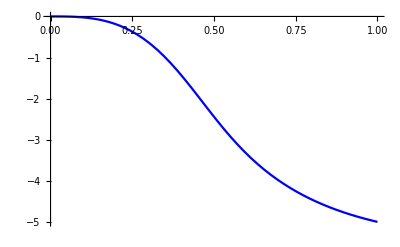

-4.99496

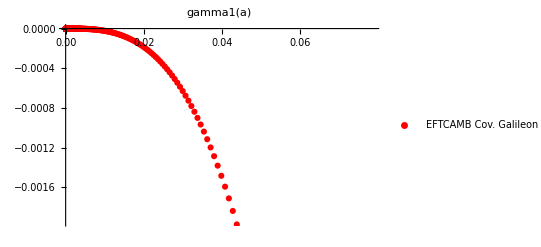

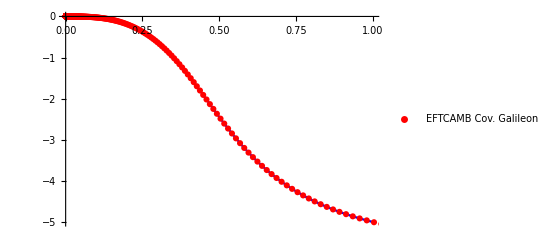

```mathematica
gamma1 = 1/(4 a^2 Subscript[H, 0]^2 s^3)(-4 (-1)^-p a^2 Subscript[c, 2] Subscript[H, DS]^2 (-1+p) p s^3 Subscript[χ, DS]^-p ℋ[a]^(2 p) φ'[a]^(2 p)+(-1)^(-p (1+1/s)) √2 a Subscript[c, 3] Subscript[H, DS] s (-s+2 p (1+s)) Subscript[χ, DS]^(-p (1+1/s)) ℋ[a]^((2 p (1+s))/s) φ'[a]^(-1+(2 p (1+s))/s) (ℋ[a] (6 (p-s+p s) φ'[a]+a s φ''[a])+a s φ'[a] ℋ'[a])+16 (-1)^(-(p (2+s))/s) Subscript[c, 5] s^2 Subscript[χ, DS]^(-(p (2+s))/s) ℋ[a]^(1+(2 p (2+s))/s) φ'[a]^(-1+(2 p (2+s))/s) (2 a (-2 s+p (2+s)) φ''[a]+s ℋ[a] (11 φ'[a]+4 a φ''[a])+a (s+2 p (2+s)) φ'[a] ℋ'[a])-4 (-1)^(-(p (2+s))/s) Subscript[c, 4] p (2+s) Subscript[χ, DS]^(-(p (2+s))/s) ℋ[a]^((2 p (2+s))/s) φ'[a]^(-2+(2 p (2+s))/s) (ℋ[a]^2 (2 (2 s^2-9 p s (2+s)+6 p^2 (2+s)^2) φ'[a]^2+a^2 s (-s+2 p (2+s)) φ''[a]^2+a s φ'[a] ((-3 s+4 p (2+s)) φ''[a]+a s φ'''[a]))+2 a^2 p s (2+s) φ'[a]^2 ℋ'[a]^2+a s ℋ[a] φ'[a] (a (s+4 p (2+s)) φ''[a] ℋ'[a]+φ'[a] ((-s+4 p (2+s)) ℋ'[a]+a s ℋ''[a]))))//Simplify;
gamma1CG = %/.DeSitterFP/.CGSubstitute/.s->2/.Xds->-7.613018601091973 H0^2/.H0-> 67.66/(2.99792458 10^5)/.c4->0.08485200961571562//Expand;
gamma1TheoryPlot=Plot[%,{a,0,1},PlotStyle->Blue]
gamma1CG/.a->1

gamma1WBGPlot=ListPlot[
gammaData⟦All,{1,2}⟧
,Joined->False
,PlotMarkers->Automatic, PlotStyle->Red,  PlotLabel->"gamma1(a)", PlotLegends->{"EFTCAMB Cov. Galileon"}
]

Show[gamma1TheoryPlot,gamma1WBGPlot]
```

## Gamma 1 Prime

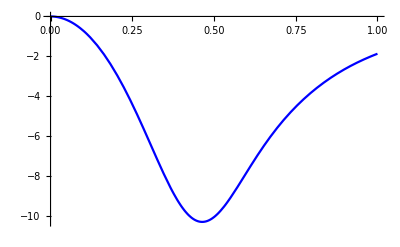

-1.86864

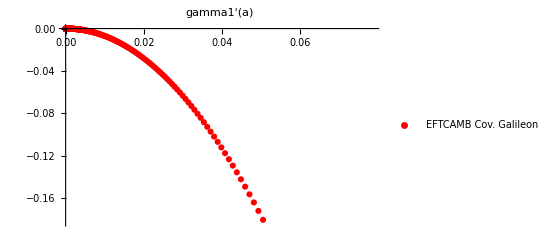

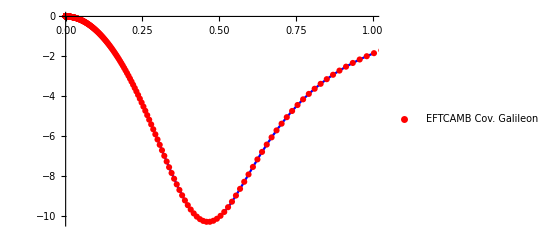

```mathematica
gamma1P =1/(4 a^3 Subscript[H, 0]^2 s^4 ℋ[a] φ'[a]^3)(-1)^(-(3 p (1+s))/s) Subscript[χ, DS]^(-(3 p (1+s))/s) (-8 (-1)^((p (3+2 s))/s) a^3 Subscript[c, 2] Subscript[H, DS]^2 (-1+p) p^2 s^4 Subscript[χ, DS]^((p (3+2 s))/s) ℋ[a]^(1+2 p) φ'[a]^(2+2 p) φ''[a]+(-1)^((2 p (1+s))/s) √2 a Subscript[c, 3] Subscript[H, DS] s (-s+2 p (1+s)) Subscript[χ, DS]^((2 p (1+s))/s) ℋ[a]^(2 (1+p+p/s)) φ'[a]^(1+(2 p (1+s))/s) (-6 s (p-s+p s) φ'[a]^2+a^2 s (-s+2 p (1+s)) φ''[a]^2+a φ'[a] (12 p (1+s) (p-s+p s) φ''[a]+a s^2 φ'''[a]))-4 (-1)^(p (2+1/s)) Subscript[χ, DS]^(p (2+1/s)) ℋ[a]^(3+(2 p (2+s))/s) φ'[a]^((2 p (2+s))/s) (-4 s (-22 Subscript[c, 5] s^3+Subscript[c, 4] p (2+s) (2 s^2-9 p s (2+s)+6 p^2 (2+s)^2)) φ'[a]^3+2 a^3 Subscript[c, 4] p s (2+s) (s^2-3 p s (2+s)+2 p^2 (2+s)^2) φ''[a]^3+a^2 s (-s+2 p (2+s)) φ'[a] φ''[a] ((-16 Subscript[c, 5] s^2+Subscript[c, 4] p (2+s) (-3 s+4 p (2+s))) φ''[a]+3 a Subscript[c, 4] p s (2+s) φ'''[a])+a φ'[a]^2 ((-8 Subscript[c, 5] s^3 (-2 s+11 p (2+s))+Subscript[c, 4] p (2+s) (3 s^3+4 p s^2 (2+s)-36 p^2 s (2+s)^2+24 p^3 (2+s)^3)) φ''[a]+a s^2 ((-16 Subscript[c, 5] s^2+Subscript[c, 4] p (2+s) (-3 s+4 p (2+s))) φ'''[a]+a Subscript[c, 4] p s (2+s) φ''''[a])))-8 (-1)^((p (3+2 s))/s) a^3 Subscript[c, 2] Subscript[H, DS]^2 (-1+p) p^2 s^4 Subscript[χ, DS]^((p (3+2 s))/s) ℋ[a]^(2 p) φ'[a]^(3+2 p) ℋ'[a]+2 (-1)^((2 p (1+s))/s) √2 a^3 Subscript[c, 3] Subscript[H, DS] p s^2 (1+s) (-s+2 p (1+s)) Subscript[χ, DS]^((2 p (1+s))/s) ℋ[a]^((2 p (1+s))/s) φ'[a]^(3+(2 p (1+s))/s) ℋ'[a]^2-16 (-1)^(p (2+1/s)) a^3 Subscript[c, 4] p^3 s (2+s)^3 Subscript[χ, DS]^(p (2+1/s)) ℋ[a]^((2 p (2+s))/s) φ'[a]^(3+(2 p (2+s))/s) ℋ'[a]^3+(-1)^((2 p (1+s))/s) √2 a^2 Subscript[c, 3] Subscript[H, DS] s (-s+2 p (1+s)) Subscript[χ, DS]^((2 p (1+s))/s) ℋ[a]^(1+(2 p (1+s))/s) φ'[a]^(2 (1+p+p/s)) (a s (s+4 p (1+s)) φ''[a] ℋ'[a]+φ'[a] (6 (-s^2-p s (1+s)+2 p^2 (1+s)^2) ℋ'[a]+a s^2 ℋ''[a]))-4 (-1)^(p (2+1/s)) a^2 s Subscript[χ, DS]^(p (2+1/s)) ℋ[a]^(1+(2 p (2+s))/s) φ'[a]^(2+(2 p (2+s))/s) ℋ'[a] (φ''[a] (-8 Subscript[c, 5] s (-2 s^2-3 p s (2+s)+2 p^2 (2+s)^2)+a Subscript[c, 4] p (2+s) (s^2+6 p s (2+s)+12 p^2 (2+s)^2) ℋ'[a])+φ'[a] ((s+2 p (2+s)) (-4 Subscript[c, 5] s (s+2 p (2+s))+Subscript[c, 4] p (2+s) (-s+4 p (2+s))) ℋ'[a]+a Subscript[c, 4] p s (2+s) (s+6 p (2+s)) ℋ''[a]))-4 (-1)^(p (2+1/s)) a Subscript[χ, DS]^(p (2+1/s)) ℋ[a]^(2+(2 p (2+s))/s) φ'[a]^(1+(2 p (2+s))/s) (a s (-s+2 p (2+s)) φ''[a]^2 (-8 Subscript[c, 5] s (-2 s+p (2+s))+3 a Subscript[c, 4] p (2+s) (s+2 p (2+s)) ℋ'[a])+s φ'[a] (a s φ'''[a] (-8 Subscript[c, 5] s (-2 s+p (2+s))+3 a Subscript[c, 4] p (2+s) (s+2 p (2+s)) ℋ'[a])+φ''[a] (2 a (-4 Subscript[c, 5] s (4 s^2+5 p s (2+s)+2 p^2 (2+s)^2)+Subscript[c, 4] p (2+s) (-3 s^2+8 p^2 (2+s)^2)) ℋ'[a]+s (8 Subscript[c, 5] s (-2 s+p (2+s))+a^2 Subscript[c, 4] p (2+s) (s+6 p (2+s)) ℋ''[a])))+φ'[a]^2 ((-4 Subscript[c, 5] s^3 (21 s+20 p (2+s))+Subscript[c, 4] p (2+s) (9 s^3-32 p s^2 (2+s)-12 p^2 s (2+s)^2+24 p^3 (2+s)^3)) ℋ'[a]+a s^2 ((-4 Subscript[c, 5] s (s+2 p (2+s))+Subscript[c, 4] p (2+s) (-s+4 p (2+s))) ℋ''[a]+a Subscript[c, 4] p s (2+s) Derivative[3][ℋ][a])))) //Simplify;
gamma1PCG = %/.DeSitterFP/.CGSubstitute/.s->2/.Xds->-7.613018601091973 H0^2/.H0-> 67.66/(2.99792458 10^5)/.c4->0.08485200961571562//Expand;
gamma1PTheoryPlot=Plot[%,{a,0,1},PlotStyle->Blue]
gamma1PCG/.a->1

gamma1PWBGPlot=ListPlot[
gammaPData⟦All,{1,2}⟧
,Joined->False
,PlotMarkers->Automatic, PlotStyle->Red,  PlotLabel->"gamma1'(a)", PlotLegends->{"EFTCAMB Cov. Galileon"}
]

Show[gamma1PTheoryPlot,gamma1PWBGPlot]
```

## Gamma 2

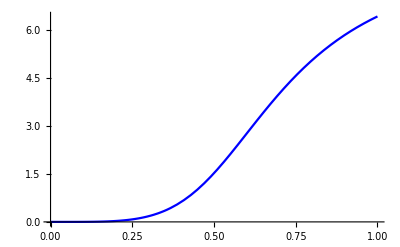

6.42934

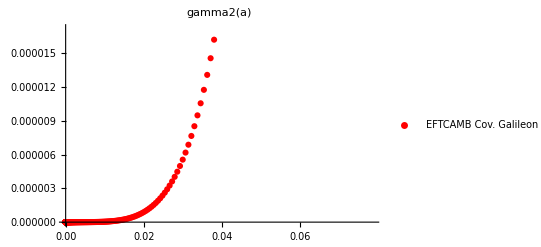

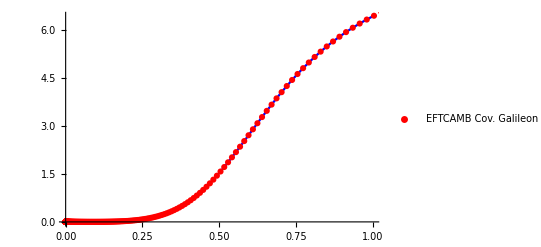

```mathematica
gamma2 = 1/(a Subscript[H, 0] s^2 φ'[a])(-1)^(-p (2+3/s)) Subscript[χ, DS]^(-p (2+3/s)) ((-1)^(1+p+(2 p)/s) √2 a Subscript[c, 3] Subscript[H, DS] s (-s+2 p (1+s)) Subscript[χ, DS]^((p (2+s))/s) ℋ[a]^((2 p (1+s))/s) φ'[a]^(1+(2 p (1+s))/s)+4 (-1)^(p (1+1/s)) Subscript[χ, DS]^(p (1+1/s)) ℋ[a]^(1+(2 p (2+s))/s) φ'[a]^((2 p (2+s))/s) (2 (-8 Subscript[c, 5] s^2+Subscript[c, 4] p (2+s) (-s+2 p (2+s))) φ'[a]+a Subscript[c, 4] p s (2+s) φ''[a])+4 (-1)^(p (1+1/s)) a Subscript[c, 4] p s (2+s) Subscript[χ, DS]^(p (1+1/s)) ℋ[a]^((2 p (2+s))/s) φ'[a]^(1+(2 p (2+s))/s) ℋ'[a])//Simplify;
gamma2CG = %/.DeSitterFP/.CGSubstitute/.s->2/.Xds->-7.613018601091973 H0^2/.H0-> 67.66/(2.99792458 10^5)/.c4->0.08485200961571562//Expand;
gamma2TheoryPlot=Plot[%,{a,0,1},PlotStyle->Blue]
gamma2CG/.a->1

gamma2WBGPlot=ListPlot[
gammaData⟦All,{1,3}⟧
,Joined->False
,PlotMarkers->Automatic, PlotStyle->Red,  PlotLabel->"gamma2(a)", PlotLegends->{"EFTCAMB Cov. Galileon"}
]

Show[gamma2TheoryPlot,gamma2WBGPlot]
```

## Gamma 2 Prime

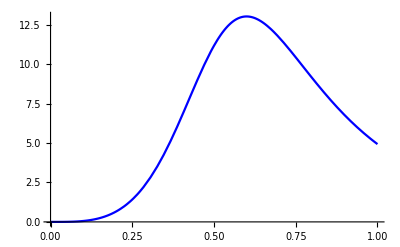

4.92848

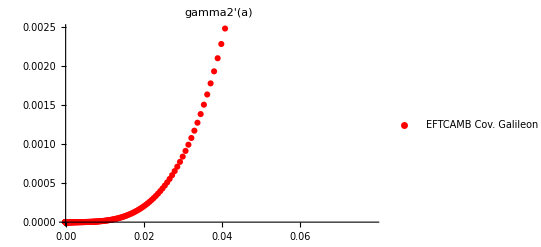

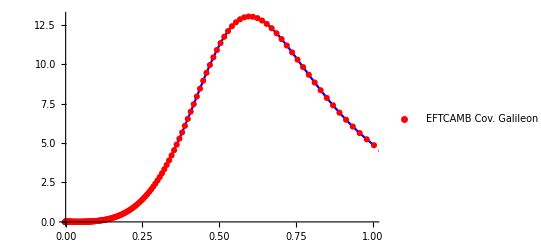

```mathematica
gamma2P = 1/(a^2 Subscript[H, 0] s^3 ℋ[a] φ'[a]^2)2 (-1)^(-p (2+3/s)) Subscript[χ, DS]^(-p (2+3/s)) ((-1)^(1+p+(2 p)/s) √2 a^2 Subscript[c, 3] Subscript[H, DS] p s (1+s) (-s+2 p (1+s)) Subscript[χ, DS]^((p (2+s))/s) ℋ[a]^(1+(2 p (1+s))/s) φ'[a]^(1+(2 p (1+s))/s) φ''[a]+2 (-1)^(p (1+1/s)) Subscript[χ, DS]^(p (1+1/s)) ℋ[a]^(2+(2 p (2+s))/s) φ'[a]^((2 p (2+s))/s) (-2 s (-8 Subscript[c, 5] s^2+Subscript[c, 4] p (2+s) (-s+2 p (2+s))) φ'[a]^2+a^2 Subscript[c, 4] p s (2+s) (-s+2 p (2+s)) φ''[a]^2+a p (2+s) φ'[a] (4 (-8 Subscript[c, 5] s^2+Subscript[c, 4] p (2+s) (-s+2 p (2+s))) φ''[a]+a Subscript[c, 4] s^2 φ'''[a]))+(-1)^(1+p+(2 p)/s) √2 a^2 Subscript[c, 3] Subscript[H, DS] p s (1+s) (-s+2 p (1+s)) Subscript[χ, DS]^((p (2+s))/s) ℋ[a]^((2 p (1+s))/s) φ'[a]^(2 (1+p+p/s)) ℋ'[a]+4 (-1)^(p (1+1/s)) a^2 Subscript[c, 4] p^2 s (2+s)^2 Subscript[χ, DS]^(p (1+1/s)) ℋ[a]^((2 p (2+s))/s) φ'[a]^(2+(2 p (2+s))/s) ℋ'[a]^2+2 (-1)^(p (1+1/s)) a Subscript[χ, DS]^(p (1+1/s)) ℋ[a]^(1+(2 p (2+s))/s) φ'[a]^(1+(2 p (2+s))/s) (a Subscript[c, 4] p s (2+s) (s+4 p (2+s)) φ''[a] ℋ'[a]+φ'[a] (2 (s+2 p (2+s)) (-8 Subscript[c, 5] s^2+Subscript[c, 4] p (2+s) (-s+2 p (2+s))) ℋ'[a]+a Subscript[c, 4] p s^2 (2+s) ℋ''[a])))//Simplify;
gamma2PCG = %/.DeSitterFP/.CGSubstitute/.s->2/.Xds->-7.613018601091973 H0^2/.H0-> 67.66/(2.99792458 10^5)/.c4->0.08485200961571562//Expand;
gamma2PTheoryPlot=Plot[%,{a,0,1},PlotStyle->Blue]
gamma2PCG/.a->1

gamma2PWBGPlot=ListPlot[
gammaPData⟦All,{1,3}⟧
,Joined->False
,PlotMarkers->Automatic, PlotStyle->Red,  PlotLabel->"gamma2'(a)", PlotLegends->{"EFTCAMB Cov. Galileon"}
]

Show[gamma2PTheoryPlot,gamma2PWBGPlot]
```

## Gamma 3

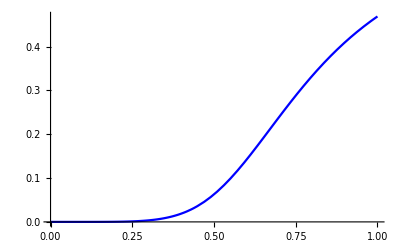

0.46857

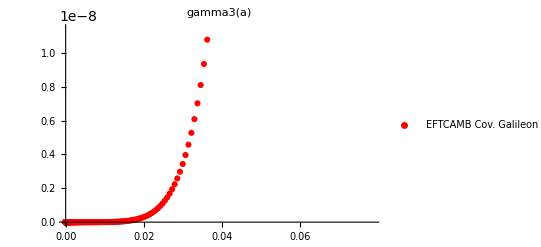

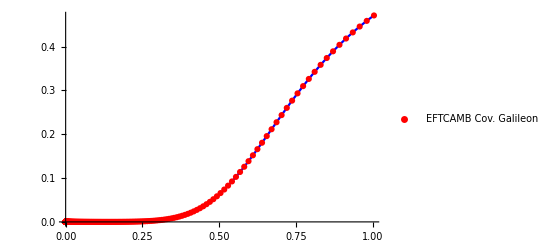

```mathematica
gamma3=(4 (-1)^(-(p (2+s))/s) (-2 Subscript[c, 5] s+Subscript[c, 4] p (2+s)) Subscript[χ, DS]^(-(p (2+s))/s) ℋ[a]^((2 p (2+s))/s) φ'[a]^((2 p (2+s))/s))/s //Simplify;
gamma3CG = %/.DeSitterFP/.CGSubstitute/.s->2/.Xds->-7.613018601091973 H0^2/.H0-> 67.66/(2.99792458 10^5)/.c4->0.08485200961571562//Expand;
gamma3TheoryPlot=Plot[%,{a,0,1},PlotStyle->Blue]
gamma3CG/.a->1

gamma3WBGPlot=ListPlot[
gammaData⟦All,{1,4}⟧
,Joined->False
,PlotMarkers->Automatic, PlotStyle->Red,  PlotLabel->"gamma3(a)", PlotLegends->{"EFTCAMB Cov. Galileon"}
]

Show[gamma3TheoryPlot,gamma3WBGPlot]
```

## Gamma 3

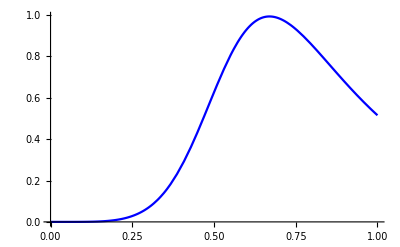

0.515208

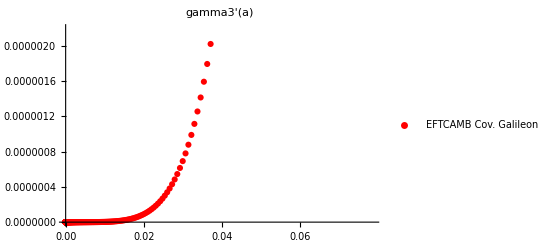

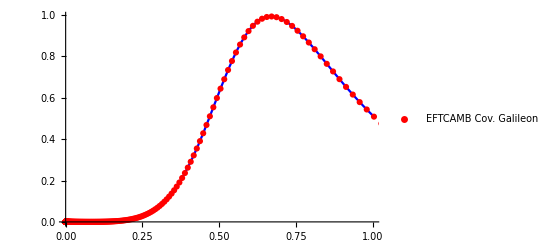

```mathematica
gamma3P= (8 (-1)^(-(p (2+s))/s) p (2+s) (-2 Subscript[c, 5] s+Subscript[c, 4] p (2+s)) Subscript[χ, DS]^(-(p (2+s))/s) ℋ[a]^(-1+(2 p (2+s))/s) φ'[a]^(-1+(2 p (2+s))/s) (ℋ[a] φ''[a]+φ'[a] ℋ'[a]))/s^2//Simplify;
gamma3PCG = %/.DeSitterFP/.CGSubstitute/.s->2/.Xds->-7.613018601091973 H0^2/.H0-> 67.66/(2.99792458 10^5)/.c4->0.08485200961571562//Expand;
gamma3PTheoryPlot=Plot[%,{a,0,1},PlotStyle->Blue]
gamma3PCG/.a->1

gamma3PWBGPlot=ListPlot[
gammaPData⟦All,{1,4}⟧
,Joined->False
,PlotMarkers->Automatic, PlotStyle->Red,  PlotLabel->"gamma3'(a)", PlotLegends->{"EFTCAMB Cov. Galileon"}
]

Show[gamma3PTheoryPlot,gamma3PWBGPlot]
```

## Gamma 4

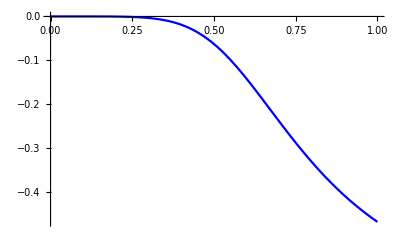

-0.46857

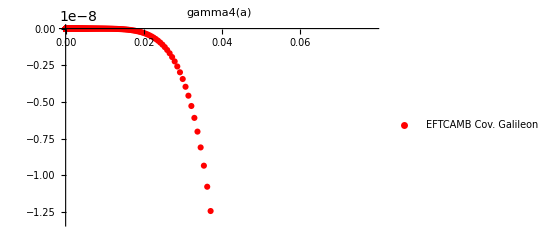

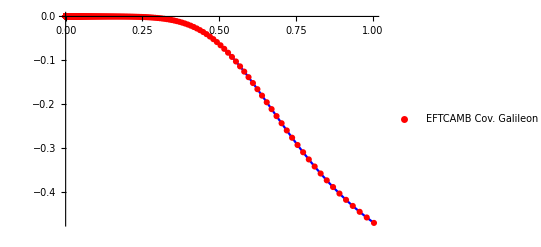

```mathematica
gamma4 = -(4 (-1)^(-(p (2+s))/s) (-2 Subscript[c, 5] s+Subscript[c, 4] p (2+s)) Subscript[χ, DS]^(-(p (2+s))/s) ℋ[a]^((2 p (2+s))/s) φ'[a]^((2 p (2+s))/s))/s//Simplify;
gamma4CG = %/.DeSitterFP/.CGSubstitute/.s->2/.Xds->-7.613018601091973 H0^2/.H0-> 67.66/(2.99792458 10^5)/.c4->0.08485200961571562//Expand;
gamma4TheoryPlot=Plot[%,{a,0,1},PlotStyle->Blue]
gamma4CG/.a->1

gamma4WBGPlot=ListPlot[
gammaData⟦All,{1,5}⟧
,Joined->False
,PlotMarkers->Automatic, PlotStyle->Red,  PlotLabel->"gamma4(a)", PlotLegends->{"EFTCAMB Cov. Galileon"}
]

Show[gamma4TheoryPlot,gamma4WBGPlot]
```

## Gamma 4 Prime

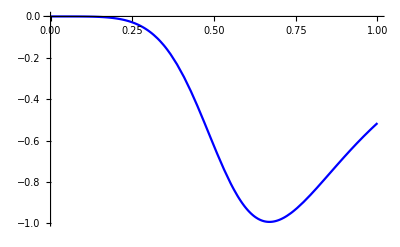

-0.515208

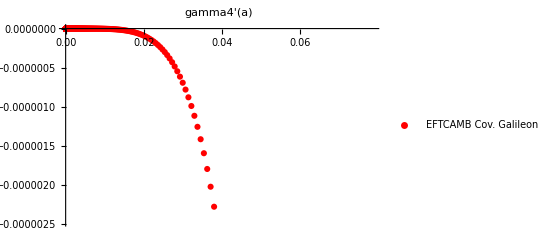

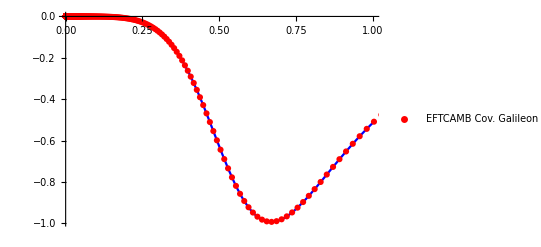

```mathematica
gamma4P = -(8 (-1)^(-(p (2+s))/s) p (2+s) (-2 Subscript[c, 5] s+Subscript[c, 4] p (2+s)) Subscript[χ, DS]^(-(p (2+s))/s) ℋ[a]^(-1+(2 p (2+s))/s) φ'[a]^(-1+(2 p (2+s))/s) (ℋ[a] φ''[a]+φ'[a] ℋ'[a]))/s^2//Simplify;
gamma4PCG = %/.DeSitterFP/.CGSubstitute/.s->2/.Xds->-7.613018601091973 H0^2/.H0-> 67.66/(2.99792458 10^5)/.c4->0.08485200961571562//Expand;
gamma4PTheoryPlot=Plot[%,{a,0,1},PlotStyle->Blue]
gamma4PCG/.a->1

gamma4PWBGPlot=ListPlot[
gammaPData⟦All,{1,5}⟧
,Joined->False
,PlotMarkers->Automatic, PlotStyle->Red,  PlotLabel->"gamma4'(a)", PlotLegends->{"EFTCAMB Cov. Galileon"}
]

Show[gamma4PTheoryPlot,gamma4PWBGPlot]
```

## Gamma 4 PrimePrime

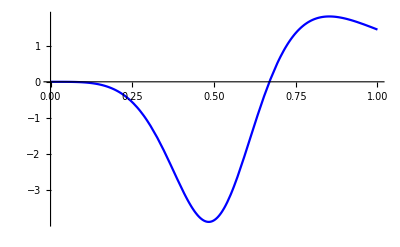

1.44263

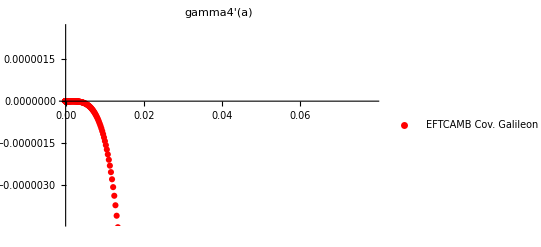

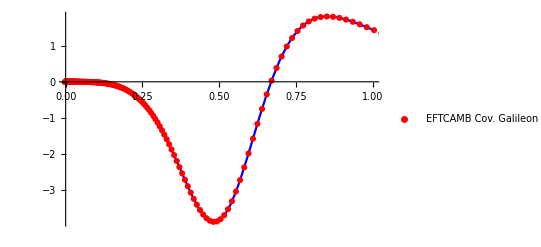

```mathematica
gamma4PP = -1/s^3 8 (-1)^(-(p (2+s))/s) p (2+s) (-2 Subscript[c, 5] s+Subscript[c, 4] p (2+s)) Subscript[χ, DS]^(-(p (2+s))/s) ℋ[a]^(-2+(2 p (2+s))/s) φ'[a]^(-2+(2 p (2+s))/s) (ℋ[a]^2 ((-s+2 p (2+s)) φ''[a]^2+s φ'[a] φ'''[a])+(-s+2 p (2+s)) φ'[a]^2 ℋ'[a]^2+ℋ[a] φ'[a] (4 p (2+s) φ''[a] ℋ'[a]+s φ'[a] ℋ''[a]))//Simplify;
gamma4PPCG = %/.DeSitterFP/.CGSubstitute/.s->2/.Xds->-7.613018601091973 H0^2/.H0-> 67.66/(2.99792458 10^5)/.c4->0.08485200961571562//Expand;
gamma4PPTheoryPlot=Plot[%,{a,0,1},PlotStyle->Blue]
gamma4PPCG/.a->1

gamma4PPWBGPlot=ListPlot[
gammaPData⟦All,{1,6}⟧
,Joined->False
,PlotMarkers->Automatic, PlotStyle->Red,  PlotLabel->"gamma4'(a)", PlotLegends->{"EFTCAMB Cov. Galileon"}
]

Show[gamma4PPTheoryPlot,gamma4PPWBGPlot]
```